## 1D AFHM: L = 10

```mathematica
Remove["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Energies = Flatten[Import["energies1d.mat"]];
```

```mathematica
StableRanks = Flatten[Import["stableranks1d.mat"]];
```

```mathematica
E1 = NumberForm[Energies[[1]],10]
```

-4.515446354

```mathematica
StableRanks[[1]]
```

2.23567

```mathematica
m = 2.068722852362781
```

2.06872

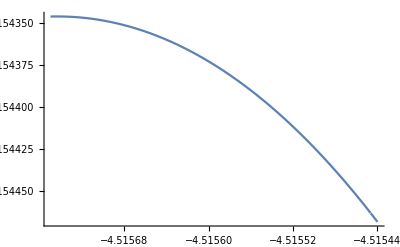

```mathematica
Plot[nu + (m Total[1/(StableRanks*(Energies-nu))])^(-1),{nu,-4.51575,-4.51544}]
```

```mathematica
(*choose broadening width*)sigma=0.1;
(*pick a fine grid over the energy range*)
energyGrid=Subdivide[Min[Energies],Max[Energies]+3 sigma,400];
(*original strong B/G/R palette*)paletteBGR={RGBColor[31/255,119/255,180/255],(*strong blue*)RGBColor[44/255,160/255,44/255],(*strong green*)RGBColor[214/255,39/255,40/255]    (*strong red*)};

(*darkening factor*)
darkFactor=0.95;

(*produce a darker version*)
palette=paletteBGR/. RGBColor[r_,g_,b_]:>RGBColor[darkFactor*r,darkFactor*g,darkFactor*b];
```

## FirstBlockPredicted

```mathematica
m = 2.068722852362781;
nustar=Replace[nu,FindRoot[1/m*Total[1/(StableRanks*(Energies-nu)^2)]-(Total[1/(StableRanks*(Energies-nu))])^2,{nu,-4.51545},MaxIterations->200]];
```

```mathematica
uprobs = 1/(StableRanks*(Energies-nustar)^2);
probs = uprobs/Total[uprobs];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
data1=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## SecondBlockPredicted

```mathematica
m = 2.216598453018552;
nustar=Replace[nu,FindRoot[1/m*Total[1/(StableRanks*(Energies-nu)^2)]-(Total[1/(StableRanks*(Energies-nu))])^2,{nu,-4.5155}]];
```

```mathematica
uprobs = 1/(StableRanks*(Energies-nustar)^2);
probs = uprobs/Total[uprobs];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
data2=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## ThirdBlockPredicted

```mathematica
m = 2.235375983187176;
nustar=Replace[nu,FindRoot[1/m*Total[1/(StableRanks*(Energies-nu)^2)]-(Total[1/(StableRanks*(Energies-nu))])^2,{nu,-4.5154469}]];
```

```mathematica
uprobs = 1/(StableRanks*(Energies-nustar)^2);
probs = uprobs/Total[uprobs];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
data3=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## MakePlot

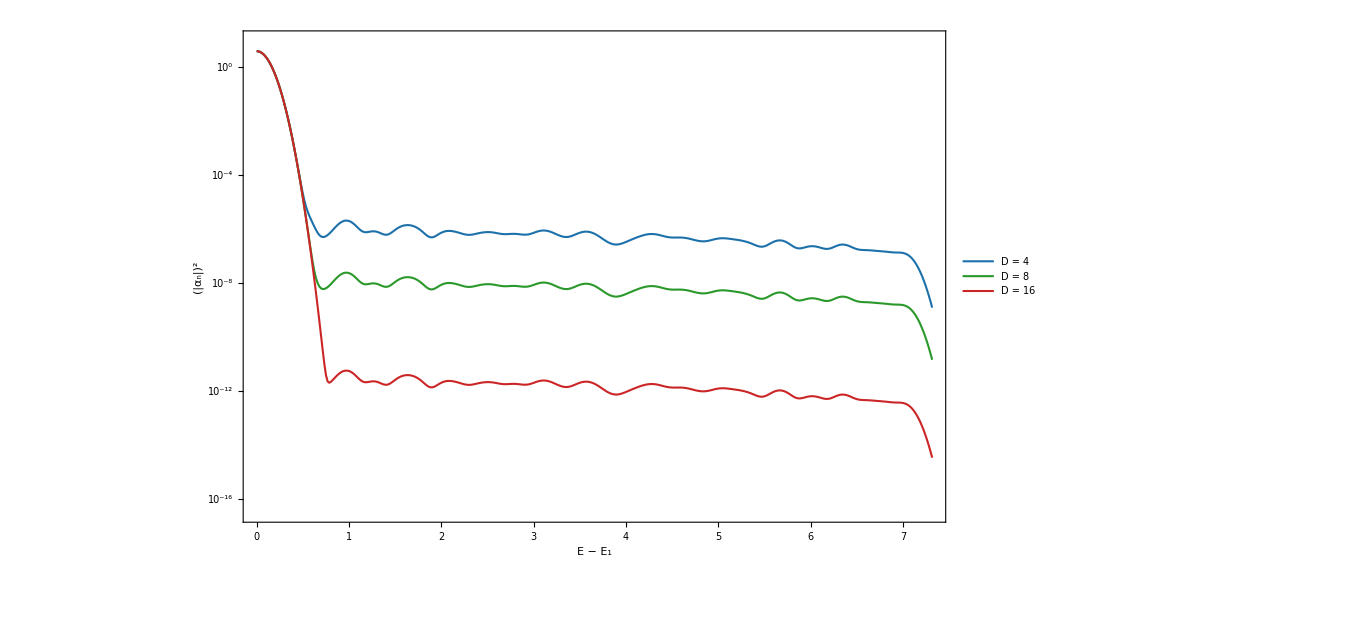

```mathematica
tickLen={0.015,0};
ymin=-16;
ymax=0;
yTicks=Table[{i,Superscript[10,i]},{i,-16,0,4}];
yTicks=Table[{i,Superscript[10,i],tickLen},{i,-16,0,4}];
xTicks=Table[{i,i,tickLen},{i,0,7,1}];
xTicksAbove=Table[{i,"",tickLen},{i,0,6,1}];
yTicksRight = Table[{i,"",tickLen},{i,-16,-4,4}];

imgSize=1000;
imagePadding={{120,10},{120,10}};

plotpredict=ListLinePlot[{data1,data2,data3},
PlotStyle->{{palette[[1]],AbsoluteThickness[1.5]},{palette[[2]],AbsoluteThickness[1.5]},{palette[[3]],AbsoluteThickness[1.5]}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[1.5]],
Axes->False,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksAbove}},
FrameLabel->{{TraditionalForm[Superscript[Row[{"|",Subscript[α,n],"|"}],2]],None},{TraditionalForm[Row[{"E"," − ",Subscript["E",1]}]],None}},LabelStyle->{FontFamily->"Times",FontSize->30},
PlotRange->{All,{-16.5,1}},
PlotTheme->"Detailed",
GridLines->None,
PlotLegends->Placed[LineLegend[{"D = 4","D = 8","D = 16"},LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameMargins->{{8,15},{0,12}}]&),LegendMarkerSize->28,LegendLayout->"Column",LabelStyle->{FontFamily->"Times",FontSize->24}],Scaled[{0.92,0.88}]],
ImageSize->imgSize,ImagePadding->imagePadding
]
```

## FirstBlockPredictedXterms

```mathematica
probs = Flatten[Import["p4.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
datax1=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## SecondBlockPredictedXterms

```mathematica
probs = Flatten[Import["p8.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
datax2=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## ThirdBlockPredictedXterms

```mathematica
probs = Flatten[Import["p16.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
datax3=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## MakePlot

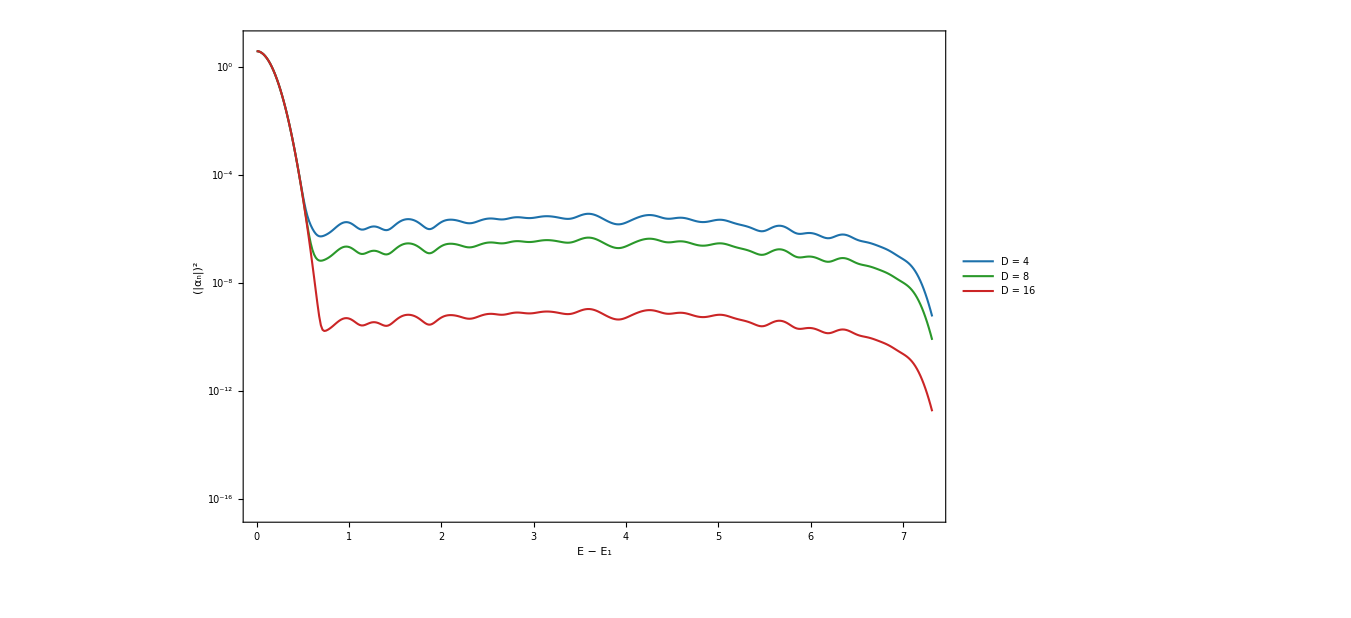

```mathematica
tickLen={0.015,0};
ymin=-16;
ymax=0;
yTicks=Table[{i,Superscript[10,i]},{i,-16,0,4}];
yTicks=Table[{i,Superscript[10,i],tickLen},{i,-16,0,4}];
xTicks=Table[{i,i,tickLen},{i,0,7,1}];
xTicksAbove=Table[{i,"",tickLen},{i,0,6,1}];
yTicksRight = Table[{i,"",tickLen},{i,-16,-4,4}];

imgSize=1000;
imagePadding={{120,10},{120,10}};

plotpredictx=ListLinePlot[{datax1,datax2,datax3},
PlotStyle->{{palette[[1]],AbsoluteThickness[1.5]},{palette[[2]],AbsoluteThickness[1.5]},{palette[[3]],AbsoluteThickness[1.5]}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[1.5]],
Axes->False,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksAbove}},
FrameLabel->{{TraditionalForm[Superscript[Row[{"|",Subscript[α,n],"|"}],2]],None},{TraditionalForm[Row[{"E"," − ",Subscript["E",1]}]],None}},LabelStyle->{FontFamily->"Times",FontSize->30},
PlotRange->{All,{-16.5,1}},
PlotTheme->"Detailed",
GridLines->None,
PlotLegends->Placed[LineLegend[{"D = 4","D = 8","D = 16"},LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameMargins->{{8,15},{0,12}}]&),LegendMarkerSize->28,LegendLayout->"Column",LabelStyle->{FontFamily->"Times",FontSize->24}],Scaled[{0.92,0.88}]],
ImageSize->imgSize,ImagePadding->imagePadding
]
```

## FirstBlockActual

```mathematica
Clear[rho]
```

```mathematica
probs = Flatten[Import["psi0_1d_D4_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
actdata1=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## SecondBlockActual

```mathematica
probs = Flatten[Import["psi0_1d_D8_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
actdata2=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## ThirdBlockActual

```mathematica
probs = Flatten[Import["psi0_1d_D16_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
actdata3=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

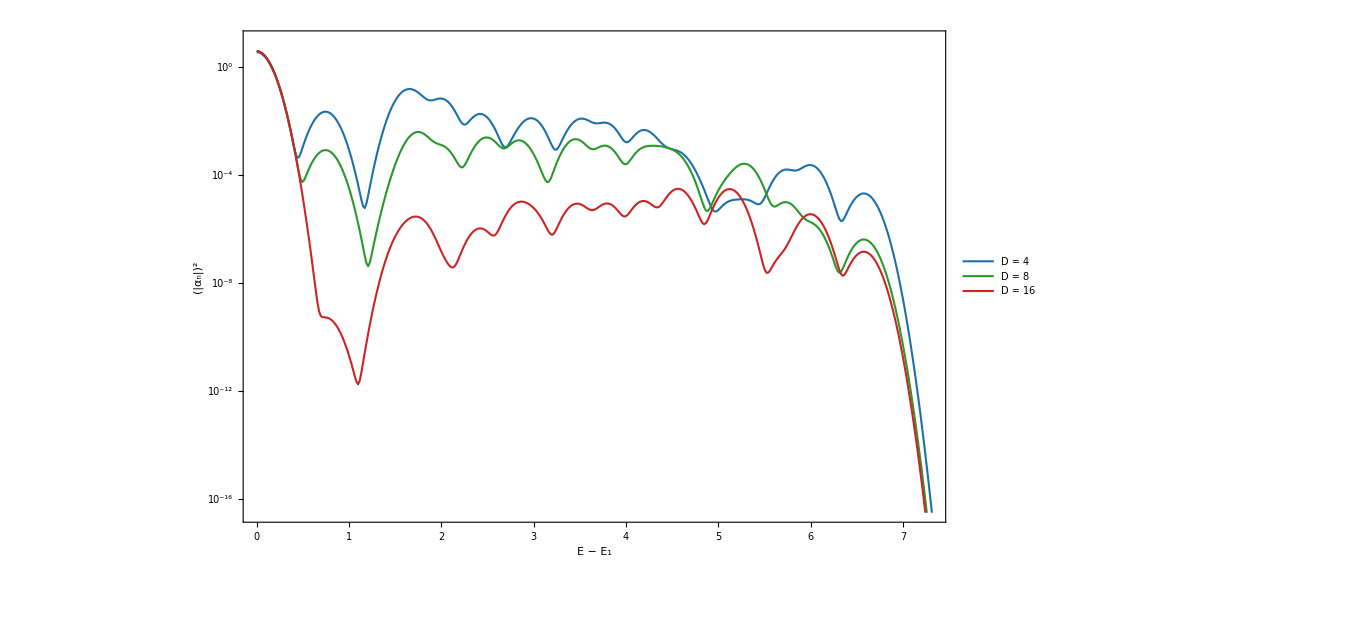

```mathematica
tickLen={0.015,0};
ymin=-16;
ymax=0;
yTicks=Table[{i,Superscript[10,i],tickLen},{i,-16,0,4}];
xTicks=Table[{i,i,tickLen},{i,0,7,1}];
xTicksAbove=Table[{i,"",tickLen},{i,0,6,1}];
yTicksRight = Table[{i,"",tickLen},{i,-16,-4,4}];

imgSize=1000;
imagePadding={{120,10},{120,10}};

plotactual=ListLinePlot[{actdata1,actdata2,actdata3},
PlotStyle->{{palette[[1]],AbsoluteThickness[1.5]},{palette[[2]],AbsoluteThickness[1.5]},{palette[[3]],AbsoluteThickness[1.5]}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[1.5]],
Axes->False,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksAbove}},
FrameLabel->{{TraditionalForm[Superscript[Row[{"|",Subscript[α,n],"|"}],2]],None},{TraditionalForm[Row[{"E"," − ",Subscript["E",1]}]],None}},LabelStyle->{FontFamily->"Times",FontSize->50},
PlotRange->{All,{-16.5,1}},
PlotTheme->"Detailed",
GridLines->None,
PlotLegends->Placed[LineLegend[{"D = 4","D = 8","D = 16"},LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameMargins->{{8,15},{0,12}}]&),LegendMarkerSize->28,LegendLayout->"Column",LabelStyle->{FontFamily->"Times",FontSize->24}],Scaled[{0.92,0.88}]],
ImageSize->imgSize,ImagePadding->imagePadding
]
```

## CombinedPlot

```mathematica
tickLen={0.015,0};
ymin=-16;
ymax=0;
yTicks=Table[{i,Superscript[10,i],tickLen},{i,-16,0,4}];
xTicks=Table[{i,i,tickLen},{i,0,7,1}];
xTicksAbove=Table[{i,"",tickLen},{i,0,7,1}];
yTicksRight = Table[{i,"",tickLen},{i,-16,0,4}];
```

### D = 4

```mathematica
imgSize=1200;
imagePadding={{200,10},{150,10}};
```

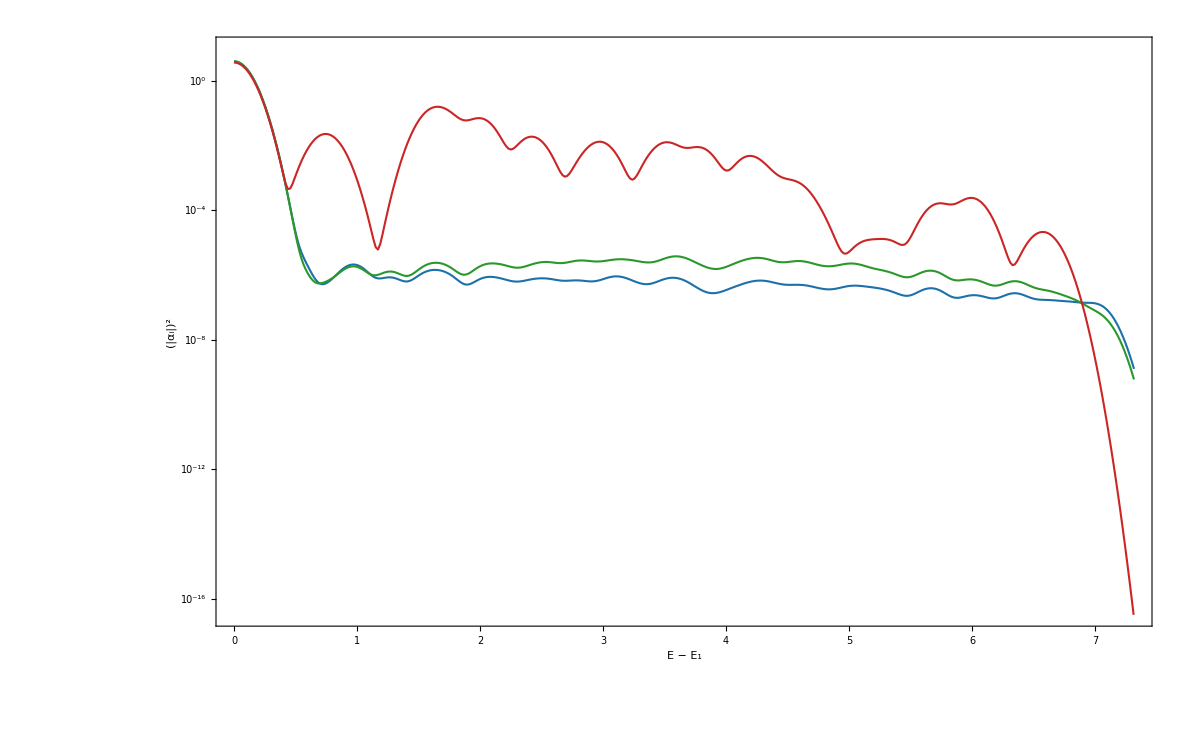

```mathematica
plotD4=ListLinePlot[{data1,datax1,actdata1},
PlotStyle->{{palette[[1]],AbsoluteThickness[1.5]},{palette[[2]],AbsoluteThickness[1.5]},{palette[[3]],AbsoluteThickness[1.5]}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[1.5]],
Axes->False,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksAbove}},
FrameLabel->{{Style[TraditionalForm[Superscript[Row[{"|",Subscript[α,i],"|"}],2]],FontFamily->"Times",FontSize->50],None},{Style[TraditionalForm[Row[{"E"," − ",Subscript["E",1]}]],FontFamily->"Times",FontSize->50],None}},LabelStyle->{FontFamily->"Times",FontSize->50},
PlotRange->{All,{-16.5,1}},
PlotTheme->"Detailed",
GridLines->None,
ImageSize->imgSize,ImagePadding->imagePadding
]
```

### D = 8

```mathematica
imgSize=1200;
imagePadding={{200,10},{150,10}};
```

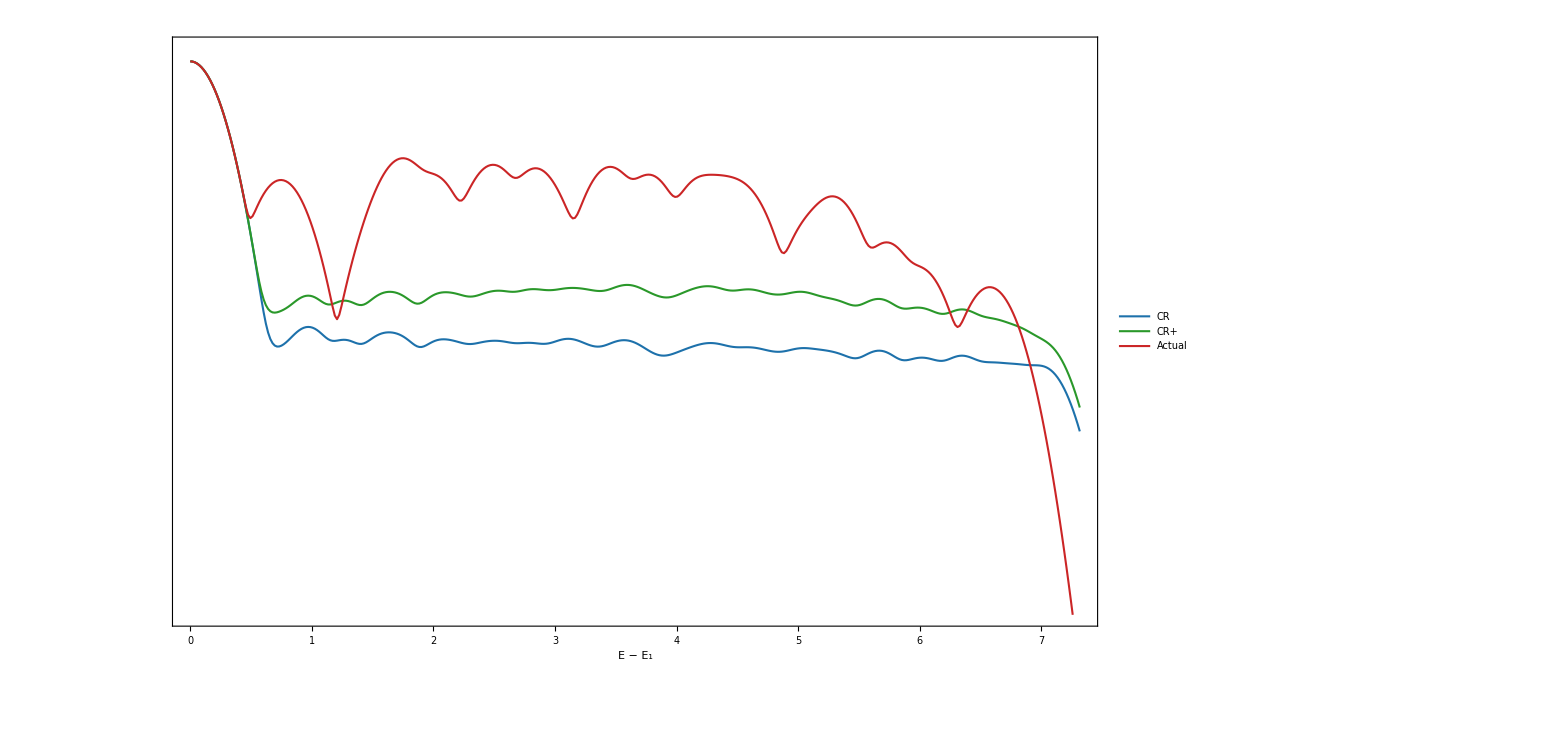

```mathematica
plotD8=ListLinePlot[{data2,datax2,actdata2},
PlotStyle->{{palette[[1]],AbsoluteThickness[1.5]},{palette[[2]],AbsoluteThickness[1.5]},{palette[[3]],AbsoluteThickness[1.5]}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[1.5]],
Axes->False,
FrameTicks->{{yTicksRight,yTicksRight},{xTicks,xTicksAbove}},
FrameLabel->{{None,None},{Style[TraditionalForm[Row[{"E"," − ",Subscript["E",1]}]],FontFamily->"Times",FontSize->50],None}},LabelStyle->{FontFamily->"Times",FontSize->50},
PlotRange->{All,{-16.5,1}},
PlotTheme->"Detailed",
GridLines->None,
PlotLegends->Placed[LineLegend[{"CR","CR+","Actual"},LegendMarkerSize->75,LegendLayout->"Row",LabelStyle->{FontFamily->"Times",FontSize->50}],Scaled[{0.5,0.25}]],
ImageSize->imgSize,ImagePadding->imagePadding
]
```

### D = 16

```mathematica
imgSize=1200;
imagePadding={{200,10},{150,10}};
```

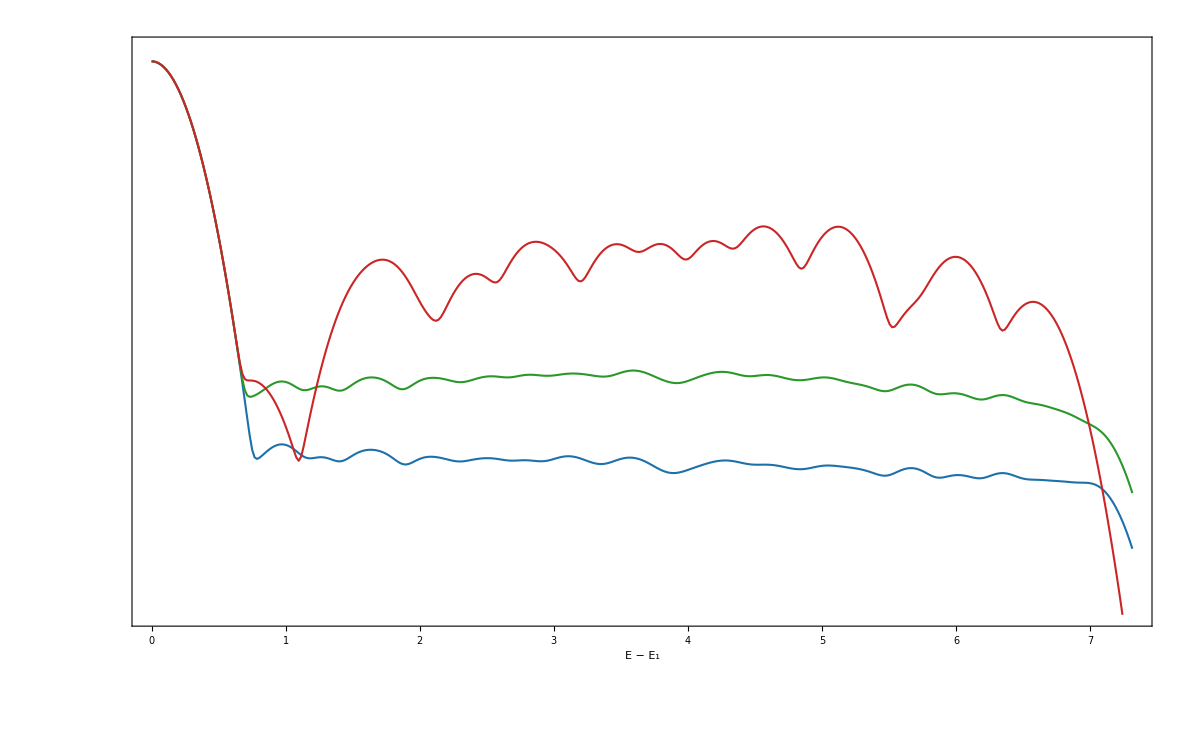

```mathematica
plotD16=ListLinePlot[{data3,datax3,actdata3},
PlotStyle->{{palette[[1]],AbsoluteThickness[1.5]},{palette[[2]],AbsoluteThickness[1.5]},{palette[[3]],AbsoluteThickness[1.5]}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[1.5]],
Axes->False,
FrameTicks->{{yTicksRight,yTicksRight},{xTicks,xTicksAbove}},
FrameLabel->{{None,None},{Style[TraditionalForm[Row[{"E"," − ",Subscript["E",1]}]],FontFamily->"Times",FontSize->50],None}},LabelStyle->{FontFamily->"Times",FontSize->50},
PlotRange->{All,{-16.5,1}},
PlotTheme->"Detailed",
GridLines->None,
ImageSize->imgSize,ImagePadding->imagePadding
]
```